```mathematica
badlist={"patient00008\\\\study2\\\\view1_frontal.jpg","patient00992\\\\study1\\\\view2_lateral.jpg","patient01282\\\\study2\\\\view1_frontal.jpg","patient01319\\\\study1\\\\view1_frontal.jpg","patient02001\\\\study4\\\\view1_frontal.jpg","patient02124\\\\study4\\\\view1_frontal.jpg","patient02484\\\\study3\\\\view1_frontal.jpg","patient02703\\\\study2\\\\view1_frontal.jpg","patient02885\\\\study1\\\\view1_frontal.jpg","patient03119\\\\study2\\\\view1_frontal.jpg","patient03304\\\\study2\\\\view1_frontal.jpg","patient03352\\\\study1\\\\view1_frontal.jpg","patient03480\\\\study1\\\\view1_frontal.jpg","patient03541\\\\study2\\\\view1_frontal.jpg","patient04102\\\\study16\\\\view2_lateral.jpg","patient04613\\\\study11\\\\view1_frontal.jpg","patient04673\\\\study1\\\\view1_frontal.jpg","patient04871\\\\study1\\\\view1_frontal.jpg","patient05205\\\\study3\\\\view1_frontal.jpg","patient05268\\\\study7\\\\view1_frontal.jpg","patient05506\\\\study4\\\\view1_frontal.jpg","patient05746\\\\study1\\\\view1_frontal.jpg","patient06263\\\\study1\\\\view2_lateral.jpg","patient06494\\\\study2\\\\view1_frontal.jpg","patient07083\\\\study3\\\\view1_frontal.jpg","patient05506\\\\study4\\\\view1_frontal.jpg","patient05746\\\\study1\\\\view1_frontal.jpg","patient07499\\\\study1\\\\view1_frontal.jpg\"","patient09739\\\\study3\\\\view1_frontal.jpg","patient11649\\\\study4\\\\view1_frontal.jpg","patient12115\\\\study13\\\\view1_frontal.jpg","patient12296\\\\study1\\\\view1_frontal.jpg","patient13077\\\\study4\\\\view2_frontal.jpg","patient13304\\\\study2\\\\view1_frontal.jpg","patient13570\\\\study30\\\\view2_lateral.jpg","patient13708\\\\study13\\\\view1_frontal.jpg","patient13861\\\\study2\\\\view1_frontal.jpg","patient13570\\\\study30\\\\view2_lateral.jpg","patient14126\\\\study1\\\\view1_frontal.jpg","patient14330\\\\study5\\\\view2_frontal.jpg","patient15759\\\\study3\\\\view1_frontal.jpg","patient16175\\\\study7\\\\view1_frontal.jpg","patient16391\\\\study5\\\\view1_frontal.jpg","patient16464\\\\study26\\\\view1_frontal.jpg","patient16558\\\\study6\\\\view1_frontal.jpg","patient16606\\\\study3\\\\view1_frontal.jpg","patient17011\\\\study15\\\\view1_frontal.jpg","patient18102\\\\study1\\\\view1_frontal.jpg","patient18639\\\\study1\\\\view1_frontal.jpg","patient19345\\\\study3\\\\view1_frontal.jpg","patient19942\\\\study1\\\\view1_frontal.jpg","patient19965\\\\study4\\\\view1_frontal.jpg","patient20028\\\\study2\\\\view1_frontal.jpg","patient20477\\\\study15\\\\view1_frontal.jpg","patient20884\\\\study7\\\\view2_lateral.jpg","patient20906\\\\study4\\\\view2_lateral.jpg","patient20964\\\\study1\\\\view1_frontal.jpg","patient21744\\\\study19\\\\view1_frontal.jpg","patient22555\\\\study2\\\\view1_frontal.jpg","patient22599\\\\study4\\\\view1_frontal.jpg","patient22770\\\\study2\\\\view1_frontal.jpg","patient23028\\\\study1\\\\view1_frontal.jpg","patient23090\\\\study2\\\\view1_frontal.jpg","patient23336\\\\study1\\\\view1_frontal.jpg","patient24206\\\\study5\\\\view2_lateral.jpg","patient24524\\\\study16\\\\view1_frontal.jpg","patient24656\\\\study2\\\\view3_lateral.jpg","patient24790\\\\study13\\\\view1_frontal.jpg","patient24838\\\\study4\\\\view1_frontal.jpg","patient24945\\\\study1\\\\view1_frontal.jpg","patient25443\\\\study1\\\\view1_frontal.jpg","patient25595\\\\study5\\\\view1_frontal.jpg","patient25826\\\\study5\\\\view1_frontal.jpg","patient26510\\\\study4\\\\view1_frontal.jpg","patient26694\\\\study16\\\\view1_frontal.jpg","patient26703\\\\study15\\\\view1_frontal.jpg","patient27546\\\\study3\\\\view2_lateral.jpg","patient28378\\\\study1\\\\view1_frontal.jpg","patient29037\\\\study6\\\\view1_frontal.jpg","patient29043\\\\study1\\\\view2_lateral.jpg","patient29212\\\\study1\\\\view1_frontal.jpg","patient29994\\\\study4\\\\view1_frontal.jpg","patient30061\\\\study1\\\\view2_frontal.jpg","patient30068\\\\study4\\\\view1_frontal.jpg","patient30337\\\\study14\\\\view1_frontal.jpg","patient30337\\\\study28\\\\view1_frontal.jpg","patient30969\\\\study4\\\\view1_frontal.jpg","patient31007\\\\study5\\\\view1_frontal.jpg","patient31164\\\\study5\\\\view1_frontal.jpg","patient31395\\\\study3\\\\view1_frontal.jpg","patient31430\\\\study1\\\\view2_lateral.jpg","patient32621\\\\study2\\\\view1_frontal.jpg","patient33458\\\\study1\\\\view1_frontal.jpg","patient33821\\\\study1\\\\view1_frontal.jpg","patient33854\\\\study8\\\\view1_frontal.jpg","patient33943\\\\study7\\\\view1_frontal.jpg","patient33971\\\\study3\\\\view1_frontal.jpg","patient34260\\\\study4\\\\view1_frontal.jpg","patient34587\\\\study5\\\\view1_frontal.jpg","patient34650\\\\study1\\\\view1_frontal.jpg","patient34712\\\\study15\\\\view1_frontal.jpg","patient34724\\\\study1\\\\view2_frontal.jpg","patient34889\\\\study4\\\\view1_frontal.jpg","patient34967\\\\study13\\\\view1_frontal.jpg","patient35100\\\\study11\\\\view1_frontal.jpg","patient35273\\\\study1\\\\view1_frontal.jpg","patient35322\\\\study3\\\\view2_frontal.jpg","patient35340\\\\study6\\\\view1_frontal.jpg","patient35469\\\\study9\\\\view1_frontal.jpg","patient35497\\\\study3\\\\view1_frontal.jpg","patient35567\\\\study5\\\\view1_frontal.jpg","patient35631\\\\study10\\\\view1_frontal.jpg","patient35785\\\\study7\\\\view1_frontal.jpg","patient35914\\\\study5\\\\view1_frontal.jpg","patient36175\\\\study13\\\\view1_frontal.jpg","patient36175\\\\study9\\\\view1_frontal.jpg","patient36236\\\\study4\\\\view1_frontal.jpg","patient36373\\\\study1\\\\view1_frontal.jpg","patient36465\\\\study12\\\\view1_frontal.jpg","patient36676\\\\study4\\\\view1_frontal.jpg","patient36711\\\\study3\\\\view1_frontal.jpg","patient37174\\\\study8\\\\view1_frontal.jpg","patient37333\\\\study6\\\\view1_frontal.jpg","patient37438\\\\study3\\\\view1_frontal.jpg","patient37462\\\\study3\\\\view1_frontal.jpg","patient37479\\\\study10\\\\view1_frontal.jpg","patient37570\\\\study4\\\\view1_frontal.jpg","patient37580\\\\study2\\\\view1_frontal.jpg","patient38208\\\\study4\\\\view1_frontal.jpg","patient38221\\\\study1\\\\view1_frontal.jpg","patient38300\\\\study5\\\\view1_frontal.jpg","patient38978\\\\study4\\\\view1_frontal.jpg","patient39016\\\\study1\\\\view1_frontal.jpg","patient39020\\\\study1\\\\view1_frontal.jpg","patient39317\\\\study4\\\\view1_frontal.jpg","patient39727\\\\study1\\\\view1_frontal.jpg","patient39956\\\\study3\\\\view1_frontal.jpg","patient40012\\\\study4\\\\view1_frontal.jpg","patient40260\\\\study1\\\\view1_frontal.jpg","patient40335\\\\study2\\\\view1_frontal.jpg","patient40396\\\\study10\\\\view1_frontal.jpg","patient40396\\\\study4\\\\view1_frontal.jpg","patient40668\\\\study1\\\\view1_frontal.jpg","patient41102\\\\study3\\\\view1_frontal.jpg","patient41219\\\\study5\\\\view1_frontal.jpg","patient41369\\\\study2\\\\view1_frontal.jpg","patient41771\\\\study3\\\\view1_frontal.jpg","patient41798\\\\study5\\\\view1_frontal.jpg","patient41839\\\\study1\\\\view2_frontal.jpg","patient42374\\\\study1\\\\view1_frontal.jpg","patient42385\\\\study2\\\\view1_frontal.jpg","patient42621\\\\study1\\\\view1_frontal.jpg","patient42911\\\\study3\\\\view1_frontal.jpg","patient43065\\\\study2\\\\view1_frontal.jpg","patient43257\\\\study2\\\\view1_frontal.jpg","patient43440\\\\study3\\\\view1_frontal.jpg","patient43661\\\\study2\\\\view1_frontal.jpg","patient43832\\\\study1\\\\view1_frontal.jpg","patient44429\\\\study6\\\\view1_frontal.jpg","patient44891\\\\study2\\\\view1_frontal.jpg","patient45031\\\\study1\\\\view1_frontal.jpg","patient45885\\\\study2\\\\view1_frontal.jpg","patient45922\\\\study3\\\\view1_frontal.jpg","patient46097\\\\study4\\\\view1_frontal.jpg","patient46361\\\\study1\\\\view1_frontal.jpg","patient46684\\\\study1\\\\view1_frontal.jpg","patient47155\\\\study1\\\\view2_frontal.jpg","patient47155\\\\study8\\\\view1_frontal.jpg","patient47345\\\\study1\\\\view1_frontal.jpg","patient47655\\\\study6\\\\view2_frontal.jpg","patient47962\\\\study6\\\\view1_frontal.jpg","patient47962\\\\study7\\\\view1_frontal.jpg","patient48087\\\\study2\\\\view1_frontal.jpg","patient48391\\\\study1\\\\view1_frontal.jpg","patient48542\\\\study1\\\\view1_frontal.jpg","patient48685\\\\study2\\\\view1_frontal.jpg","patient48845\\\\study2\\\\view1_frontal.jpg","patient49035\\\\study1\\\\view2_frontal.jpg","patient49158\\\\study2\\\\view2_frontal.jpg","patient49199\\\\study3\\\\view1_frontal.jpg","patient49507\\\\study1\\\\view2_frontal.jpg","patient50339\\\\study1\\\\view1_frontal.jpg","patient51007\\\\study1\\\\view1_frontal.jpg","patient51401\\\\study1\\\\view1_frontal.jpg","patient51479\\\\study1\\\\view1_frontal.jpg","patient51759\\\\study1\\\\view1_frontal.jpg","patient51813\\\\study1\\\\view1_frontal.jpg","patient52121\\\\study3\\\\view1_frontal.jpg","patient52307\\\\study2\\\\view1_frontal.jpg","patient52670\\\\study1\\\\view1_frontal.jpg","patient52804\\\\study2\\\\view1_frontal.jpg","patient53174\\\\study1\\\\view1_frontal.jpg","patient53493\\\\study2\\\\view1_frontal.jpg","patient54181\\\\study1\\\\view1_frontal.jpg","patient54502\\\\study3\\\\view1_frontal.jpg","patient54569\\\\study2\\\\view1_frontal.jpg","patient55002\\\\study1\\\\view1_frontal.jpg","patient55690\\\\study2\\\\view1_frontal.jpg","patient55720\\\\study2\\\\view1_frontal.jpg","patient55832\\\\study2\\\\view1_frontal.jpg","patient56384\\\\study1\\\\view1_frontal.jpg","patient56497\\\\study2\\\\view1_frontal.jpg","patient57201\\\\study2\\\\view1_frontal.jpg","patient57460\\\\study2\\\\view1_frontal.jpg","patient57629\\\\study1\\\\view1_frontal.jpg","patient58044\\\\study3\\\\view1_frontal.jpg","patient58483\\\\study7\\\\view1_frontal.jpg","patient58679\\\\study1\\\\view1_frontal.jpg","patient58838\\\\study1\\\\view1_frontal.jpg","patient59412\\\\study1\\\\view1_frontal.jpg","patient59804\\\\study1\\\\view1_frontal.jpg","patient59816\\\\study1\\\\view1_frontal.jpg","patient60655\\\\study1\\\\view1_frontal.jpg","patient61792\\\\study1\\\\view1_frontal.jpg","patient61792\\\\study2\\\\view1_frontal.jpg","patient62562\\\\study1\\\\view1_frontal.jpg","patient62625\\\\study1\\\\view1_frontal.jpg","patient63181\\\\study2\\\\view1_frontal.jpg","patient63308\\\\study1\\\\view1_frontal.jpg"};
(*badlist=Import["c:\\users\\Public\\listbad.txt","List"];*)
traindir="d:\\CheXpert-v1.0-small\\train\\";
(*testfiles=Select[FileNames["*.jpg",traindir,Infinity],!DirectoryQ[#]&];
testfiles >> traintestfiles.m;*)
<<traintestfiles.m
testfiles=%;
nfiles=Length[testfiles];
fullnamebad= FileNameJoin[{traindir,#}] & /@ badlist;
normalfiles=Select[testfiles,!MemberQ[fullnamebad,#]&];
Length[normalfiles]
```

{d:\CheXpert-v1.0-small\train\patient00001\study1\._view1_frontal.jpg,d:\CheXpert-v1.0-small\train\patient00001\study1\view1_frontal.jpg,d:\CheXpert-v1.0-small\train\patient00002\study1\view1_frontal.jpg,d:\CheXpert-v1.0-small\train\patient00002\study1\view2_lateral.jpg,d:\CheXpert-v1.0-small\train\patient00002\study2\view1_frontal.jpg,d:\CheXpert-v1.0-small\train\patient00003\study1\view1_frontal.jpg,223403,d:\CheXpert-v1.0-small\train\patient64536\study2\view1_frontal.jpg,d:\CheXpert-v1.0-small\train\patient64537\study1\view1_frontal.jpg,d:\CheXpert-v1.0-small\train\patient64537\study2\view1_frontal.jpg,d:\CheXpert-v1.0-small\train\patient64538\study1\view1_frontal.jpg,d:\CheXpert-v1.0-small\train\patient64539\study1\view1_frontal.jpg,d:\CheXpert-v1.0-small\train\patient64540\study1\view1_frontal.jpg}
 |  |  |  |

223200

```mathematica
N[219/8]
```

27.375

```mathematica
Dimensions[fullnamebad]
```

{219}
 |  |  |  |

Import::nffil: File d:\CheXpert-v1.0-small\train\patient07499\study1\view1_frontal.jpg" not found during Import.

ImageResize::imginv: Expecting an image or graphics instead of $Failed.

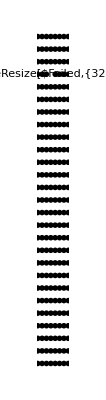

```mathematica
GraphicsGrid[Table[ImageResize[Import[fullnamebad[[(x-1)*8+y]]],{32,32}],{x,1,27},{y,1,8}],ImageSize->Full]
```